# PERCENT

```mathematica
{ol500c24h,ol500c24hkeep,ol500c24hkill,ol500c24hmem,oltyp}=Import["C:\\Users\\muxy1\\OneDrive\\桌面\\Modeling paper\\ol500c24htest.mx"];
```

```mathematica
{hpgen1,hpgen10,hpgen50,hpgen90,hpgen99,hpkeep1,hpkeep10,hpkeep50,hpkeep90,hpkeep99,hpmem1,hpmem10,hpmem50,hpmem90,hpmem99,hpkill1,hpkill10,hpkill50,hpkill90,hpkill99,hptyp1,hptyp10,hptyp50,hptyp90,hptyp99}=Import["C:\\Users\\muxy1\\OneDrive\\桌面\\Modeling paper\\hp500c24hpercent.mx"];
```

```mathematica
{hpgen3000,hpgen6000,hmugen7000,hmugen14000,hpkeep3000,hpkeep6000,hmukeep7000,hmukeep14000,hpkill3000,hpkill6000,hmukill7000,hmukill14000}=Import["C:\\Users\\muxy1\\OneDrive\\桌面\\Modeling paper\\hphmularge.mx"];
```

```mathematica
{hpkill3000,hpkill6000,hptyp3000,hptyp6000}=Import["C:\\Users\\mxy\\Desktop\\Modeling paper\\hplargecorrect.mx"];
```

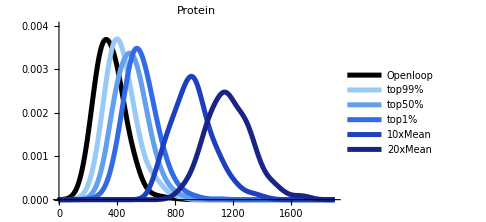

```mathematica
SmoothHistogram[{ol500c24h[[1]][[1]]/ol500c24h[[1]][[6]],hpgen1[[1]][[1]]/hpgen1[[1]][[6]],hpgen50[[1]][[1]]/hpgen50[[1]][[6]],hpgen99[[1]][[1]]/hpgen99[[1]][[6]],hpgen3000[[1]][[1]]/hpgen3000[[1]][[6]],hpgen6000[[1]][[1]]/hpgen6000[[1]][[6]]},50,PlotRange->{{0,1900},{0,0.004}},PlotLegends->{"Openloop","top99%","top50%","top1%","10xMean","20xMean"},PlotLabel->Style["Protein",Black,16],PlotStyle->{Directive[Black,Thickness[0.01]],Directive[RGBColor["#97caf7"],Thickness[0.01]],Directive[RGBColor["#639fef"],Thickness[0.01]],Directive[RGBColor["#326be5"],Thickness[0.01]],Directive[RGBColor["#1e40bd"],Thickness[0.01]],Directive[RGBColor["#192586"],Thickness[0.01]]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

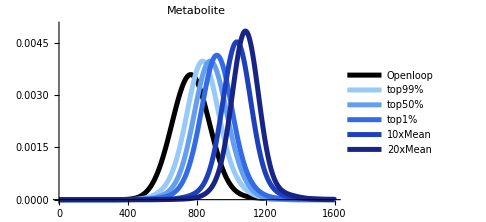

```mathematica
SmoothHistogram[{ol500c24h[[1]][[4]]/ol500c24h[[1]][[6]],hpgen1[[1]][[4]]/hpgen1[[1]][[6]],hpgen50[[1]][[4]]/hpgen50[[1]][[6]],hpgen99[[1]][[4]]/hpgen99[[1]][[6]],hpgen3000[[1]][[4]]/hpgen3000[[1]][[6]],hpgen6000[[1]][[4]]/hpgen6000[[1]][[6]]},70,PlotRange->{{0,1600},{0,0.005}},PlotLegends->{"Openloop","top99%","top50%","top1%","10xMean","20xMean"},PlotLabel->Style["Metabolite",Black,16],PlotStyle->{Directive[Black,Thickness[0.01]],Directive[RGBColor["#97caf7"],Thickness[0.01]],Directive[RGBColor["#639fef"],Thickness[0.01]],Directive[RGBColor["#326be5"],Thickness[0.01]],Directive[RGBColor["#1e40bd"],Thickness[0.01]],Directive[RGBColor["#192586"],Thickness[0.01]]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

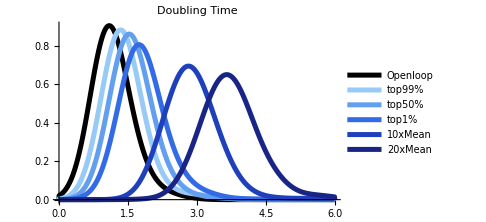

```mathematica
SmoothHistogram[{Log[2]/ol500c24h[[1]][[5]],Log[2]/hpgen1[[1]][[5]],Log[2]/hpgen50[[1]][[5]],Log[2]/hpgen99[[1]][[5]],Log[2]/hpgen3000[[1]][[5]],Log[2]/hpgen6000[[1]][[5]]},0.35,PlotRange->{{0,6},Automatic},PlotLegends->{"Openloop","top99%","top50%","top1%","10xMean","20xMean"},PlotLabel->Style["Doubling Time",Black,16],PlotStyle->{Directive[Black,Thickness[0.01]],Directive[RGBColor["#97caf7"],Thickness[0.01]],Directive[RGBColor["#639fef"],Thickness[0.01]],Directive[RGBColor["#326be5"],Thickness[0.01]],Directive[RGBColor["#1e40bd"],Thickness[0.01]],Directive[RGBColor["#192586"],Thickness[0.01]]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

```mathematica
hpmem3000=metabproteinmemfast[hpkeep3000];
```

```mathematica
hpmem6000=metabproteinmemfast[hpkeep6000];
```

```mathematica
ol500c24hmem=metabproteinmemfast[ol500c24hkeep];
```

```mathematica
{hpmem1,hpmem10,hpmem50,hpmem90,hpmem99,hpmem3000,hpmem6000}=Parallelize[{metabproteinmemfast[hpkeep1],metabproteinmemfast[hpkeep10],metabproteinmemfast[hpkeep50],metabproteinmemfast[hpkeep90],metabproteinmemfast[hpkeep99],metabproteinmemfast[hpkeep3000],metabproteinmemfast[hpkeep6000]}];
```

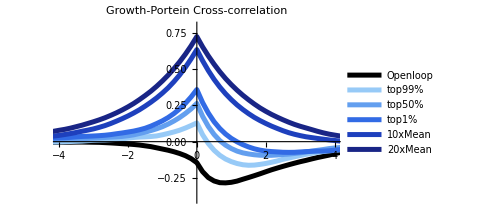

```mathematica
ListLinePlot[{ol500c24hmem[[4]],hpmem1[[4]],hpmem50[[4]],hpmem99[[4]],hpmem3000[[4]],hpmem6000[[4]]},PlotRange->{{-4,4},{-0.4,0.8}},PlotLegends->{"Openloop","top99%","top50%","top1%","10xMean","20xMean"},PlotLabel->Style["Growth-Portein Cross-correlation",Black,16],PlotStyle->{Directive[Black,Thickness[0.01]],Directive[RGBColor["#97caf7"],Thickness[0.01]],Directive[RGBColor["#639fef"],Thickness[0.01]],Directive[RGBColor["#326be5"],Thickness[0.01]],Directive[RGBColor["#1e40bd"],Thickness[0.01]],Directive[RGBColor["#192586"],Thickness[0.01]]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

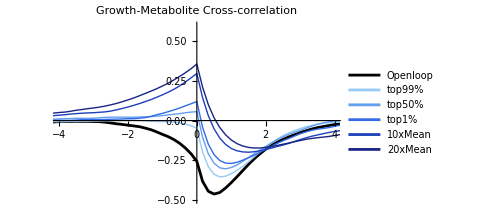

```mathematica
ListLinePlot[{ol500c24hmem[[5]],hpmem1[[5]],hpmem50[[5]],hpmem99[[5]],hpmem3000[[5]],hpmem6000[[5]]},PlotRange->{{-4,4},{-0.5,0.6}},PlotLegends->{"Openloop","top99%","top50%","top1%","10xMean","20xMean"},PlotLabel->Style["Growth-Metabolite Cross-correlation",Black,16],PlotStyle->{Directive[Black],Directive[RGBColor["#97caf7"],Thick],Directive[RGBColor["#639fef"],Thick],Directive[RGBColor["#326be5"],Thick],Directive[RGBColor["#1e40bd"],Thick],Directive[RGBColor["#192586"],Thick]},AxesStyle->Directive[Black, ],ImageSize->Medium]
```

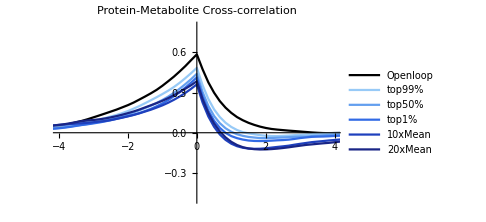

```mathematica
ListLinePlot[{ol500c24hmem[[6]],hpmem1[[6]],hpmem50[[6]],hpmem99[[6]],hpmem3000[[6]],hpmem6000[[6]]},PlotRange->{{-4,4},{-0.5,0.8}},PlotLegends->{"Openloop","top99%","top50%","top1%","10xMean","20xMean"},PlotLabel->Style["Protein-Metabolite Cross-correlation",Black,16],PlotStyle->{Directive[Black],Directive[RGBColor["#97caf7"],Thick],Directive[RGBColor["#639fef"],Thick],Directive[RGBColor["#326be5"],Thick],Directive[RGBColor["#1e40bd"],Thick],Directive[RGBColor["#192586"],Thick]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

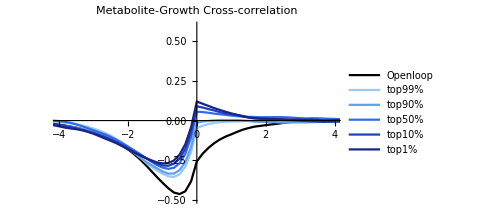

```mathematica
ListLinePlot[{ol500c24hmem[[5]],hpmem1[[5]],hpmem10[[5]],hpmem50[[5]],hpmem90[[5]],hpmem99[[5]]},PlotRange->{{-4,4},{-0.5,0.6}},PlotLegends->{"Openloop","top99%","top90%","top50%","top10%","top1%"},PlotLabel->Style["Metabolite-Growth Cross-correlation",Black,16],PlotStyle->{Directive[Black],Directive[RGBColor["#97caf7"],Thick],Directive[RGBColor["#639fef"],Thick],Directive[RGBColor["#326be5"],Thick],Directive[RGBColor["#1e40bd"],Thick],Directive[RGBColor["#192586"],Thick]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

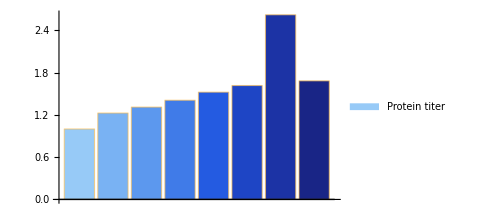

```mathematica
BarChart[{oltyp[[2]]/oltyp[[2]],hptyp1[[2]]/oltyp[[2]],hptyp10[[2]]/oltyp[[2]],hptyp50[[2]]/oltyp[[2]],hptyp90[[2]]/oltyp[[2]],hptyp99[[2]]/oltyp[[2]],hptyp3000[[2]]/oltyp[[2]],hptyp6000[[2]]/oltyp[[2]]},ChartLegends->{"Protein titer"},ChartStyle->{RGBColor["#97caf7"],RGBColor["#79b2f3"],RGBColor["#5c98ee"],
RGBColor["#407be8"],
RGBColor["#245be1"],
RGBColor["#1e45c5"],
RGBColor["#1c33a5"],
RGBColor["#192586"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

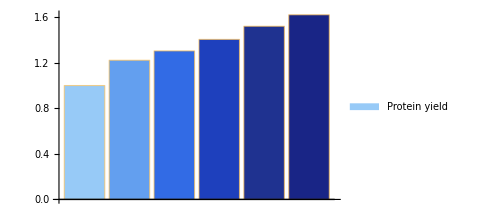

```mathematica
BarChart[{oltyp[[5]]/oltyp[[5]],hptyp1[[5]]/oltyp[[5]],hptyp10[[5]]/oltyp[[5]],hptyp50[[5]]/oltyp[[5]],hptyp90[[5]]/oltyp[[5]],hptyp99[[5]]/oltyp[[5]]},ChartLegends->{"Protein yield"},ChartStyle->{RGBColor["#97caf7"],
RGBColor["#639fef"],
RGBColor["#326be5"],
RGBColor["#1e40bd"],
RGBColor["#1f3290"],
RGBColor["#192586"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

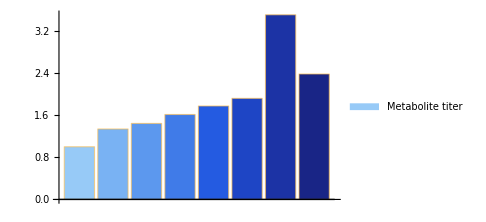

```mathematica
BarChart[{oltyp[[4]]/oltyp[[4]],hptyp1[[4]]/oltyp[[4]],hptyp10[[4]]/oltyp[[4]],hptyp50[[4]]/oltyp[[4]],hptyp90[[4]]/oltyp[[4]],hptyp99[[4]]/oltyp[[4]],hptyp3000[[4]]/oltyp[[4]],hptyp6000[[4]]/oltyp[[4]]},ChartLegends->{"Metabolite titer"},ChartStyle->{RGBColor["#97caf7"],RGBColor["#79b2f3"],RGBColor["#5c98ee"],
RGBColor["#407be8"],
RGBColor["#245be1"],
RGBColor["#1e45c5"],
RGBColor["#1c33a5"],
RGBColor["#192586"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

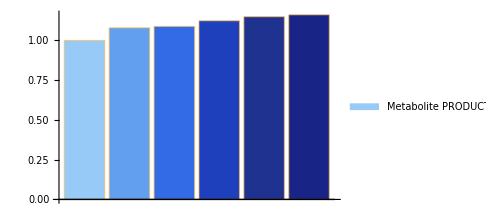

```mathematica
BarChart[{oltyp[[9]]/oltyp[[9]],hptyp1[[9]]/oltyp[[9]],hptyp10[[9]]/oltyp[[9]],hptyp50[[9]]/oltyp[[9]],hptyp90[[9]]/oltyp[[9]],hptyp99[[9]]/oltyp[[9]]},ChartLegends->{"Metabolite PRODUCTIVITY"},ChartStyle->{RGBColor["#97caf7"],
RGBColor["#639fef"],
RGBColor["#326be5"],
RGBColor["#1e40bd"],
RGBColor["#1f3290"],
RGBColor["#192586"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

```mathematica
ListLinePlot[{oltyp[[1]],hptyp1[[1]],hptyp10[[1]],hptyp50[[1]],hptyp90[[1]],hptyp99[[1]],hptyp3000[[1]],hptyp6000[[1]]},PlotLegends->{"Openloop","top99%","top90%","top50%","top10%","top1%","10xMean","20xMean"},PlotStyle->{Black,Lighter[RGBColor["#97caf7"]],RGBColor["#97caf7"],
RGBColor["#639fef"],
RGBColor["#326be5"],
RGBColor["#1e40bd"],
RGBColor["#1f3290"],
RGBColor["#192586"]},AxesStyle->Directive[Black, 16],PlotLabel->"protein titer" ,
ImageSize->Medium]
```

-Graphics-

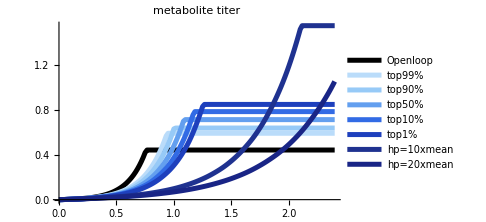

```mathematica
ListLinePlot[{oltyp[[3]]/10^16,hptyp1[[3]]/10^16,hptyp10[[3]]/10^16,hptyp50[[3]]/10^16,hptyp90[[3]]/10^16,hptyp99[[3]]/10^16,hptyp3000[[3]]/10^16,hptyp6000[[3]]/10^16},PlotLabel->"metabolite titer",PlotLegends->{"Openloop","top99%","top90%","top50%","top10%","top1%","hp=10xmean","hp=20xmean"},PlotStyle->{Directive[Black,Thickness[0.01]],Directive[Lighter[RGBColor["#97caf7"]],Thickness[0.01]],Directive[RGBColor["#97caf7"],Thickness[0.01]],
Directive[RGBColor["#639fef"],Thickness[0.01]],
Directive[RGBColor["#326be5"],Thickness[0.01]],
Directive[RGBColor["#1e40bd"],Thickness[0.01]],
Directive[RGBColor["#1f3290"],Thickness[0.01]],
Directive[RGBColor["#192586"],Thickness[0.01]]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

```mathematica
ListLinePlot[{{Transpose@{ol500c24hkill[[All,1]],ol500c24hkill[[All,19]]}},{Transpose@{hpkill1[[All,1]],hpkill1[[All,19]]}},{Transpose@{hpkill10[[All,1]],hpkill10[[All,19]]}},{Transpose@{hpkill50[[All,1]],hpkill50[[All,19]]}},{Transpose@{hpkill90[[All,1]],hpkill90[[All,19]]}},Transpose@{hpkill99[[All,1]],hpkill99[[All,19]]},{Transpose@{hpkill3000[[All,1]],hpkill3000[[All,19]]}},{Transpose@{hpkill6000[[All,1]],hpkill6000[[All,19]]}}},PlotStyle->{Black,Lighter[RGBColor["#97caf7"]],RGBColor["#97caf7"],
RGBColor["#639fef"],
RGBColor["#326be5"],
RGBColor["#1e40bd"],
RGBColor["#1f3290"],
RGBColor["#192586"]},AxesStyle->Directive[Black, 16],ImageSize->Medium, Axes->{True,True}]
```

ListLinePlot[{1},PlotStyle→{GrayLevel[0],RGBColor[0.7281045751633987, 0.861437908496732, 0.9790849673202614],RGBColor[0.592156862745098, 0.792156862745098, 0.9686274509803922],RGBColor[0.38823529411764707, 0.6235294117647059, 0.9372549019607843],RGBColor[0.19607843137254902, 0.4196078431372549, 0.8980392156862745],RGBColor[0.11764705882352941, 0.25098039215686274, 0.7411764705882353],RGBColor[0.12156862745098039, 0.19607843137254902, 0.5647058823529412],RGBColor[0.09803921568627451, 0.1450980392156863, 0.5254901960784314]},AxesStyle→Directive[GrayLevel[0],16],ImageSize→Medium,Axes→{True,True}]
 |  |  |  |

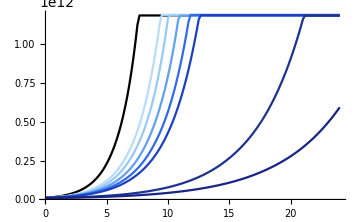

```mathematica
ListLinePlot[{Transpose@{ol500c24hkill[[All,1]],ol500c24hkill[[All,12]]},Transpose@{hpkill1[[All,1]],hpkill1[[All,12]]},Transpose@{hpkill10[[All,1]],hpkill10[[All,12]]},Transpose@{hpkill50[[All,1]],hpkill50[[All,12]]},Transpose@{hpkill90[[All,1]],hpkill90[[All,12]]},Transpose@{hpkill99[[All,1]],hpkill99[[All,12]]},Transpose@{hpkill3000[[All,1]],hpkill3000[[All,12]]},Transpose@{hpkill6000[[All,1]],hpkill6000[[All,12]]}},PlotStyle->{Black,Lighter[RGBColor["#97caf7"]],RGBColor["#97caf7"],
RGBColor["#639fef"],
RGBColor["#326be5"],
RGBColor["#1e40bd"],
RGBColor["#1f3290"],
RGBColor["#192586"]},AxesStyle->Directive[Black, 16],ImageSize->Medium, Axes->{True,True}]
```

```mathematica
a=RandomVariate[GeometricDistribution[0.05]]
```

14